```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica"];
Get["ctmc`"]
Get["utils`"]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 2 binding sites ***)

(*Edge lists and weights*)
edges2={{5,1},{1,5},{2,6},{6,2},{1,2},{1,3},{2,4},{3,1},{3,4},{4,2},{6,5}};
weights2={c*kboff2,kuoff,kuon,c*kbon2,kon1b,c*kboff,c*kbon,kuoff2,kon2b,kuon2,koffu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&kboff>0&&kboff2>0&&kuon>0&&kuon2>0&&kbon>0&&kbon2>0&&kon1b>0&&kuoff>0&&kuoff2>0&&kon2b>0&&koffu>0;
```

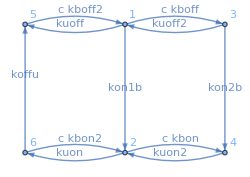

```mathematica
(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{6,5},{2,1},{4,3}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Variance rate*)
onInd={0,1,0,1,0,1};
var=VarianceRate[Q2,onInd];
```

```mathematica
(*Sharpness*)
piOn=onInd.ss2;
```

```mathematica
dpiOn=D[pion,{c,1}];
sharp=c*dpion;
```

```mathematica
Not/@onInd
```

{0,1,0,1,0,1}

{!0,!1,!0,!1,!0,!1}

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F25 = Fon[[2,5]][[1]];
F45 = Fon[[4,5]][[1]];
F65 = Fon[[6,5]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {5,1,3};
onStates = {6,2,4};
F5on = LaplaceTransformToSetByState[Q2,5,onStates,s1];
FoffOn = F5on[[2]][[1]]*F25 +F5on[[3]][[1]]*F45+F5on[[1]][[1]]*F65;
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];

meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
τfun[c_?NumericQ,kboff_?NumericQ,kboff2_?NumericQ,kbon_?NumericQ,kbon2_?NumericQ,koffu_?NumericQ,kon1b_?NumericQ,kon2b_?NumericQ,kuoff_?NumericQ,kuoff2_?NumericQ,kuon_?NumericQ,kuon2_?NumericQ ]:=Evaluate[τ];
```

```mathematica
With[{c=5,kboff=0.05,kboff2=0.05,kuoff=0.2,kuoff2=0.2,kbon=0.5,kbon2=0.5,kuon=1,kuon2=1,konu=5,koffu=1,kon1b=1,kon2b=1},Evaluate[meanTonLt]]
```

13.4224

```mathematica
expr1=FoffOn;
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2]
```

(c^2 kboff kboff2 koffu kon2b kuon kuon2+c kboff2 koffu kon1b kon2b kuon kuon2+c kboff2 koffu kon1b kuoff2 kuon kuon2+c kboff2 koffu kon1b kuon kuon2 s1+c kboff2 koffu kon1b kon2b kuon s2+c kboff2 koffu kon1b kuoff2 kuon s2+c kboff2 koffu kon1b kuon s1 s2)/((c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+c^2 kboff kboff2 s1+c kboff2 kon1b s1+c kboff kon2b s1+c kboff2 kon2b s1+kon1b kon2b s1+kon2b kuoff s1+c kboff2 kuoff2 s1+kon1b kuoff2 s1+kuoff kuoff2 s1+c kboff s1^2+c kboff2 s1^2+kon1b s1^2+kon2b s1^2+kuoff s1^2+kuoff2 s1^2+s1^3) (koffu kuon kuon2+c^2 kbon kbon2 s2+c kbon koffu s2+koffu kuon s2+c kbon2 kuon2 s2+koffu kuon2 s2+kuon kuon2 s2+c kbon s2^2+c kbon2 s2^2+koffu s2^2+kuon s2^2+kuon2 s2^2+s2^3))

```mathematica
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
```

```mathematica
Pjoint/.{t1->0.1,t2->1,c->1., c2->1., kboff->2.,kboff2->2., kbon->2., kbon2->2.,konb->3.,konu->1.,kuon->1.,kuon2->1.,kon1b->1.,kon2b->4.,koffu->3.,kuoff->2.,kuoff2->2.,kuon->1.}
```

0.0310402

```mathematica
integrand =D[Pjoint,{c,1}]^2/Pjoint;
```

```mathematica
integrandSimpl=integrand//.{Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,1]->A1,
Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,2]->A2,
Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,3]->A3,
Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,1]->B1,
Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,2]->B2,
Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,3]->B3,
c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2->C1,
c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2->C2,
c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2->C3,
2 c kboff kboff2+kboff2 kon1b+kboff kon2b+kboff2 kon2b+kboff2 kuoff2->C4,
-2 c kboff kboff2 kon2b-kboff2 kon1b kon2b-kboff2 kon1b kuoff2->C5,
2 c kbon kbon2+kbon koffu+kbon2 kuon2->C6,
c kbon+c kbon2+koffu+kuon+kuon2->C7};
```

```mathematica
integrandSimpl[[12]][[1]][[1]]//Simplify
```

```mathematica
integrandSimpl[[11]]//Simplify
```

```mathematica
expr=integrandSimpl[[12]][[1]][[8]][[11]]//.{kboff+kboff2->C8,kbon+kbon2->C9}
```

```mathematica
exprSmall=Collect[Total[simpleTerms],{A1, A2, A3, B1, B2, B3},(*collect with respect to x and y*)
Factor      (*factor each collected coefficient*)];
```

```mathematica
assoc=GroupBy[simpleTerms,Denominator,(*key:the denominator*)Total[Numerator/@#]&              (*value:sum of numerators*)];

combinedTerms=KeyValueMap[Function[{den,num},num/den],assoc]
```

```mathematica
integrandSimpl/.{t1->0.1,t2->1,c->1., c2->1., kboff->2.,kboff2->2., kbon->2., kbon2->2.,konb->3.,konu->1.,kuon->1.,kuon2->1.,kon1b->1.,kon2b->4.,koffu->3.,kuoff->2.,kuoff2->2.,kuon->1.,A1->2.,B1->2.1,A2->2.2,B2->2.3,A3->2.4,B3->2.5,C1->2.,C2->2.1,C3->2.2,C4->2.3,C5->2.4,C6->2.5}
```

4.78358

```mathematica
vars=Complement[DeleteDuplicates@Cases[integrandSimpl,_Symbol,{0,Infinity}],{E,I,Pi}]//Sort;
pattern1=Sequence@@(#<>"_?NumericQ"&/@ToString/@vars);
pattern2={#,_Real}&/@vars;
pattern3="N["<>#<>"]"&/@ToString/@vars;
vars
```

{A1,A2,A3,B1,B2,B3,c,C1,C2,C3,C4,C5,C6,kboff,kboff2,kbon,kbon2,koffu,kon1b,kon2b,kuoff2,kuon,kuon2,t1,t2}

```mathematica
integrandC=Compile[{{A1,_Real},{A2,_Real},{A3,_Real},{B1,_Real},{B2,_Real},{B3,_Real},{c,_Real},{C1,_Real},{C2,_Real},{C3,_Real},{C4,_Real},{C5,_Real},{C6,_Real},{kboff,_Real},{kboff2,_Real},{kbon,_Real},{kbon2,_Real},{koffu,_Real},{kon1b,_Real},{kon2b,_Real},{kuoff2,_Real},{kuon,_Real},{kuon2,_Real},{t1,_Real},{t2,_Real}},
Evaluate[integrandSimpl],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
integrandNum[A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,c_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,C4_?NumericQ,C5_?NumericQ,C6_?NumericQ,kboff_?NumericQ,kboff2_?NumericQ,kbon_?NumericQ,kbon2_?NumericQ,koffu_?NumericQ,kon1b_?NumericQ,kon2b_?NumericQ,kuoff2_?NumericQ,kuon_?NumericQ,kuon2_?NumericQ,t1_?NumericQ,t2_?NumericQ]:=integrandC[N[A1],N[A2],N[A3],N[B1],N[B2],N[B3],N[c],N[C1],N[C2],N[C3],N[C4],N[C5],N[C6],N[kboff],N[kboff2],N[kbon],N[kbon2],N[koffu],N[kon1b],N[kon2b],N[kuoff2],N[kuon],N[kuon2],N[t1],N[t2]];
```

```mathematica
integrandNum[1.1,1.4,1.5,1.2,1.9,2.2,1.1,1.4,1.5,1.2,1.9,2.2,2.,1.4,1.5,2.6,3.7,2.8,1.9,3.0,2.1,3.2,2.3,1.4,1.5]
```

19470.8

```mathematica
ClearAll[FisherFast];
ClearAll[FisherSafe];
(*kboff2,kuoff,kuon,c*kbon2,kon1b,c*kboff,c*kbon,kuoff2,kon2b,kuon2,koffu*)
FisherFast[c_?NumericQ,kboff2_?NumericQ,kuoff_?NumericQ,kuon_?NumericQ,kbon2_?NumericQ,kon1b_?NumericQ,kboff_?NumericQ,kbon_?NumericQ,kuoff2_?NumericQ,kon2b_?NumericQ,kuon2_?NumericQ,koffu_?NumericQ ]:=Module[{τeval,integral,A1,A2,A3,B1,B2,B3,C1,C2,C3,C4,C5,C6},
τeval=τfun[c,kboff,kboff2,kbon,kbon2,koffu,kon1b,kon2b,kuoff,kuoff2,kuon,kuon2];
A1=Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,1];
A2=Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,2];
A3=Root[c^2 kboff kboff2 kon2b+c kboff2 kon1b kon2b+c kboff2 kon1b kuoff2+(c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2) #1+(c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2) #1^2+#1^3&,3];
B1=Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,1];B2=Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,2];
B3=Root[koffu kuon kuon2+(c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2) #1+(c kbon+c kbon2+koffu+kuon+kuon2) #1^2+#1^3&,3];
C1=c^2 kboff kboff2+c kboff2 kon1b+c kboff kon2b+c kboff2 kon2b+kon1b kon2b+kon2b kuoff+c kboff2 kuoff2+kon1b kuoff2+kuoff kuoff2;
C2=c kboff+c kboff2+kon1b+kon2b+kuoff+kuoff2;
C3=c^2 kbon kbon2+c kbon koffu+koffu kuon+c kbon2 kuon2+koffu kuon2+kuon kuon2;
C4=2 c kboff kboff2+kboff2 kon1b+kboff kon2b+kboff2 kon2b+kboff2 kuoff2;
C5=-2 c kboff kboff2 kon2b-kboff2 kon1b kon2b-kboff2 kon1b kuoff2;
C6=2 c kbon kbon2+kbon koffu+kbon2 kuon2;
integral=NIntegrate[integrandNum[A1,A2,A3,B1,B2,B3,c,C1,C2,C3,C4,C5,C6,kboff,kboff2,kbon,kbon2,koffu,kon1b,kon2b,kuoff2,kuon,kuon2,t1,t2],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential"},
PrecisionGoal->5,
MinRecursion->3,
MaxRecursion->10];
integral*c^2/τeval];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
kmin =0.005;
kmax = 5;
kdl=0.0888;
(*        c,kboff2,kuoff,kuon,kbon2,kon1b,kboff,kbon,kuoff2,kon2b,kuon2,koffu*)
FisherSafe[0.1,kdl,kdl,kmin,kmin,kmax,kmin,kmax,kmin,kmin,kmax,kmax]
```

0.00300824

```mathematica
{data, params}=GetData["20250509/2bs-fir-free-c0"];
```

```mathematica
ClearAll[vars]
ClearAll[rates]
```

```mathematica
kc=16;
kg=1;
kw=1;
skc=ToString[kc];
skg=ToString[kg];
skw=ToString[kw];
nparams=11;
logrates=data[skc,skg,skw][[;;nparams]];
rates=Table[10^logrates[[i]],{i,1,nparams}];
vars={kboff2,kuoff,kuon,kbon2,kon1b,kboff,kbon,kuoff2,kon2b,kuon2,koffu};

c0=params["betas"][[kc]];

lb=Table[kmin,{i,1,nparams}];
ub=Table[kmax,{i,1,nparams}];
ub[[1]]=2*kdl;
ub[[4]]=2*kdl;
ub[[6]]=kdl;
ub[[7]]=kdl;
ub[[8]]=2*kmax;
ub[[10]]=2*kmax;


FisherSafe@@input
data[skc,skg,skw][[nparams+1]]
```

1.39732

1.2984

```mathematica
ClearAll[constraints]
constraints=Table[lb[[i]]<=vars[[i]]<=ub[[i]],{i,1,nparams}]
```

{0.005≤kboff2≤0.1776,0.005≤kuoff≤5,0.005≤kuon≤5,0.005≤kbon2≤0.1776,0.005≤kon1b≤5,0.005≤kboff≤0.0888,0.005≤kbon≤0.0888,0.005≤kuoff2≤10,0.005≤kon2b≤5,0.005≤kuon2≤10,0.005≤koffu≤5}

```mathematica
FindMaximum[{
FisherSafe[c0,kboff2,kuoff,kuon,kbon2,kon1b,kboff,kbon,kuoff2,kon2b,kuon2,koffu],
constraints},
Table[{vars[[i]],rates[[i]]},{i,1,nparams}],
AccuracyGoal->3,
PrecisionGoal->3,
MaxIterations->10
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 6 iterations.

{0.987085,{kboff2→0.0387768,kuoff→3.4842,kuon→4.12265,kbon2→0.0530944,kon1b→0.0120756,kboff→0.0503285,kbon→0.0397375,kuoff2→0.637961,kon2b→4.26694,kuon2→3.58497,koffu→4.09344}}

```mathematica
rates
```

{0.0541925,4.40821,4.61333,0.00175545,0.00674974,0.0361109,0.0041057,0.00930819,4.92382,8.04452,4.99952}